# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time unit μs *)
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(* duration for moving operations: Split and Combine*)
DurMove-><|"Alice"->4, "Bob"->5|>,

(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,

(* Readout: fidelity. It has bitflip error *)
FidRead-><|"Alice"->0.98, "Bob"->0.99|>,
DurRead-><|"Alice"->20, "Bob"->20|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual) *)
FidSingleXY-><|"Alice"->0.98, "Bob"->0.99|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{0.2,0.8},"Bob"->{0.1,0.9}|>,
(* rabi frequency on single rotations in MHz *)
RabiFreq-><|"Alice"->5, "Bob"->5 |>,


(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>
};
```

Questlink takes initial indices; thus, passive noise is incorrect. Manually added for every gate? 

native gates:  Init, Read, Rx, Ry, C[Z], Ent[node1,node2], SWAP, SplitZ, CombZ  

Zone1 :prepare, store(?), detect
Zone2 :prepare, store, detect, logic
Zone3 :prepare, store, detect, logic
Zone4 :remote entangle

{{0,{Damp_0[0.99],Depol_0[0.0294079],Deph_0[0.0475813],Depol_1[0.0294079],Deph_1[0.0475813],Depol_2[0.0294079],Deph_2[0.0475813],Depol_3[0.0294079],Deph_3[0.0475813]},{}},{4,{Damp_4[0.98],Depol_4[0.0333277],Deph_4[0.0525803],Depol_5[0.0333277],Deph_5[0.0525803],Depol_6[0.0333277],Deph_6[0.0525803],Depol_7[0.0333277],Deph_7[0.0525803]},{}},{9,{Kraus_1[{{{0.989949,0.},{0.,0.989949}},{{0.141421,0.},{0.,0.141421}}}],M_1},{}}}

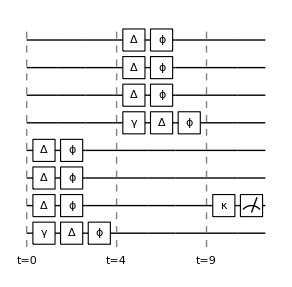

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
InsertCircuitNoise[{Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[SplitZ, 2,3]["Alice",4],Subscript[SplitZ, 2,3]["Bob",4],Subscript[Read, 2]["Alice"]},dev,ReplaceAliases->True]
DrawCircuit[%,dev[NumTotalQubits]]
dev@ShowNodes
```

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 1,2]["Alice",3],Subscript[SplitZ, 1,2]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[CombZ, 1,2]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 3,4]["Alice",3]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[CombZ, 2,3]["Bob",2]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 2,3]["Alice",4],Subscript[SplitZ, 2,3]["Bob",4]},dev,ReplaceAliases->False]
DrawCircuit@%
```

{{0,{SplitZ_(1,2)},{}},{1,{SplitZ_(5,6)},{}}}

-Graphics-